```mathematica
Lx=Ly=32;
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,Dimensions[FlatSite][[1]],2}];
```

```mathematica
(** 32x32 system **)
```

```mathematica
a3= Import["/home/archisman/Documents/GitHub/quasicrystals/results/magnetic field/Model in PRL paper/32x32tx=0.csv"];
```

```mathematica
blist3=Re[ToExpression[#]&/@a3];
```

```mathematica
Dimensions[blist3]
```

{206848,2}

```mathematica
Dimensions[blist3][[1]]/101
```

2048

```mathematica
blist3Sorted=Sort[blist3];
```

```mathematica
aaa31={}
```

{}

```mathematica
aaa32={}
```

{}

```mathematica
Do[aaa31 = Append[aaa31,blist3Sorted[[(2048)/2+3+2048*n]]],{n,0,100}]
```

```mathematica
Do[aaa32 = Append[aaa32,blist3Sorted[[(2048)/2+1+2048*n]]],{n,0,100}]
```

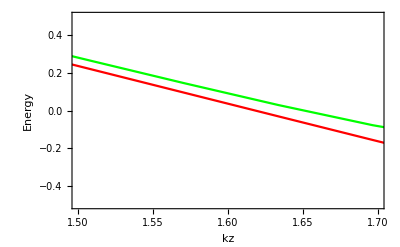

```mathematica
Show[ListPlot[aaa31,PlotRange->  {{1.5,1.7},{-0.5,0.5}},PlotStyle->{PointSize[0.01],Green},Joined-> True],ListPlot[aaa32,PlotRange-> {{1.5,1.7},{-0.5,0.5}},PlotStyle->{PointSize[0.01],Red},Joined-> True],AxesLabel-> {"kz","Energy"},Frame-> True]
```

```mathematica
Clear[aaa3]
```

```mathematica
aaa3 = aaa31;
```

```mathematica
Show[ListPlot[blist3,PlotRange-> { {-3.14,3.14} ,{-2.5,2.5}},PlotStyle->PointSize[0.01]],ListPlot[aaa3,PlotRange-> All,PlotStyle->{PointSize[0.01],Red},Joined-> True],FrameLabel-> {"kz","Energy"},Frame-> True,BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

-Graphics-

```mathematica
(** quasicrtstal 1 **)
```

```mathematica
a= Import["/home/archisman/Documents/GitHub/quasicrystals/results/magnetic field/Model in PRL paper/quasicrystal/FibonEnergies32x32-linUp+14linDn-4.csv"];
```

```mathematica
blist=Re[ToExpression[#]&/@a];
```

```mathematica
Dimensions[blist]
```

{115342,2}

```mathematica
115342/101
```

1142

```mathematica
blist[[1142*70+1142/2]]
```

{1.25664,12.5981}

```mathematica
blistSorted=Sort[blist];
```

```mathematica
aaa={}
```

{}

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+14
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-4
```

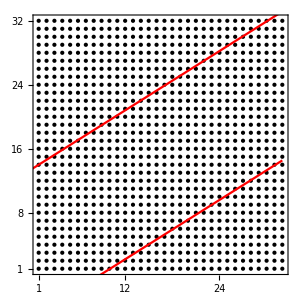

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"},{32,"32"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"},{32,"32"}},None}},
ImageSize-> 300,AspectRatio-> 1
]
```

```mathematica
aaa={}
```

{}

```mathematica
Do[aaa = Append[aaa,blistSorted[[(1142)/2+1+1142*n]]],{n,0,100}]
```

```mathematica
Show[ListPlot[aaa,PlotRange-> All,PlotStyle->{PointSize[0.01],Red}],AxesLabel-> {"kz","Energy"},Frame-> True];
```

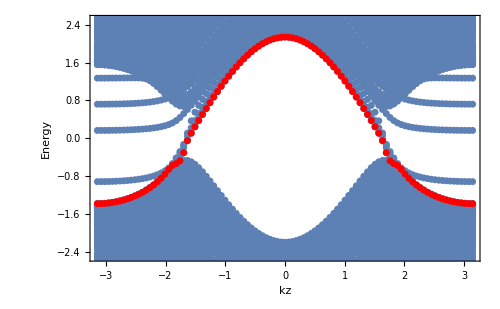

```mathematica
Show[ListPlot[blist,PlotRange-> { {-3.14,3.14} ,{-2.5,2.5}},PlotStyle->PointSize[0.01]],ListPlot[aaa,PlotRange-> All,PlotStyle->{PointSize[0.01],Red}],FrameLabel-> {"kz","Energy"},Frame-> True,BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize-> 500]
```

```mathematica
(** quasicrtstal 2 **)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+4
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+2
```

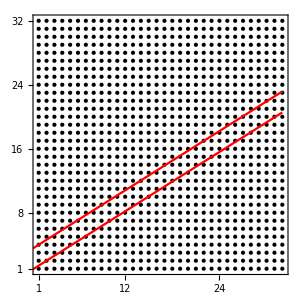

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"},{32,"32"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"},{32,"32"}},None}},
ImageSize-> 300,AspectRatio-> 1
]
```

```mathematica
a2= Import["/home/archisman/Documents/GitHub/quasicrystals/results/magnetic field/Model in PRL paper/quasicrystal/FibonEnergies32x32-linUp+4linDn+2.csv"];
```

```mathematica
blist2=Re[ToExpression[#]&/@a2];
```

```mathematica
Dimensions[blist2]
```

{16766,2}

```mathematica
16766/101
```

166

```mathematica
blist2Sorted=Sort[blist2];
```

```mathematica
aaa2={}
```

{}

```mathematica
Do[aaa2 = Append[aaa2,blist2Sorted[[(166)/2+1+166*n]]],{n,0,100}]
```

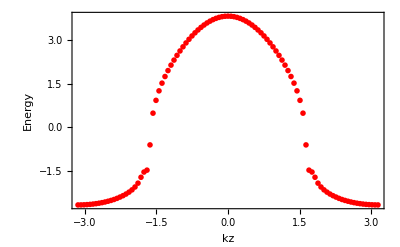

```mathematica
Show[ListPlot[aaa2,PlotRange-> All,PlotStyle->{PointSize[0.01],Red}],AxesLabel-> {"kz","Energy"},Frame-> True]
```

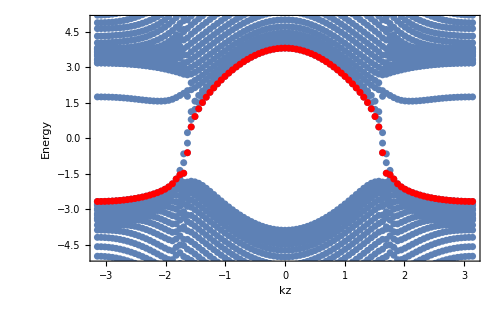

```mathematica
Show[ListPlot[blist2,PlotRange-> { {-3.14,3.14} ,{-5,5}},PlotStyle->PointSize[0.01]],ListPlot[aaa2,PlotRange-> All,PlotStyle->{PointSize[0.01],Red}],FrameLabel-> {"kz","Energy"},Frame-> True,BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize-> 500]
```